## Introduction

This document is the companion file to the thesis “NAME THESIS HERE” by Kolja Kuijpers
I will try to be as complete as possible in documenting the steps I am taking.
This document will be uploaded to github.com and my aim is to keep is publically available for as long as possible.

## Setup

In this section I perform the intial setup for the rest of the document. This can be run all at once.

### Launching xCoba

xCoba is the backbone of the computations in the first few sections. It is an amazing package that can rapidly perform tensor calculations. We load the package here, this package can be downloaded from: http://xact.es/download.html

xCoba is built on top of xTensor. xTensor allows for general tensor calculations. xCoba adds the functionality to define explicit metrics and to calculations on them.

```mathematica
<<xact`xCoba`;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.5, {2021,8,29}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### Setting up the manifold and metric

With xCoba launched,  we first need to define a manifold followed by a Metric.

```mathematica
DefManifold[M,4, IndexRange[a,n]];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefMetric[-1,Metricg[-a,-b],CD,{";","∇"}];
```

** DefTensor: Defining symmetric metric tensor Metricg[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonMetricg[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetraMetricg[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetraMetricg†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density DetMetricg[]. Determinant.

In the following we add some preferences to the output of Tensor calculations, and we tell the package to treat certain symbols as constants with DefConstantSymbol[].

```mathematica
$CovDFormat="Prefix";
PrintAs[RiemannCD]^="R";
PrintAs[WeylCD]^="C";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
PrintAs[Metricg]^="g";PrintAs[DetMetricg]^="g";
```

```mathematica
DefConstantSymbol[α];
DefConstantSymbol[β];
DefConstantSymbol[γ];
DefConstantSymbol[G];
```

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol γ.

** DefConstantSymbol: Defining constant symbol G.

### Defining an explicit metric

We now want to specify an explicit metric, i.e. the general static, spherically symmetric metric.

#### Setting up the chart

First we define two characters to be treated as scalar functions by the package. 
NOTE: In the thesis we use lower case h and f. These are, however, reserved as tensor indices so in the notebook file we will instead use uppercase H and F.

We define a chart with DefChart[]

```mathematica
DefScalarFunction[H];
DefScalarFunction[F];
```

** DefScalarFunction: Defining scalar function H.

** DefScalarFunction: Defining scalar function F.

```mathematica
DefChart[sph, M, {0,1,2,3}, {t[],r[],θ[],ϕ[]}];
```

** DefChart: Defining chart sph.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sph.

** DefMapping: Defining inverse mapping isph.

** DefTensor: Defining mapping differential tensor disph[-a,ispha].

** DefTensor: Defining mapping differential tensor dsph[-a,spha].

** DefBasis: Defining basis sph. Coordinated basis.

** DefCovD: Defining parallel derivative PDsph[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsph[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsph[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsph[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsph[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsph[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsph[-a,-b,-c,-d].

#### Setting the metric

We now make an  tensor to be our metric. The  tensor is defined on the chart we defined above.
With CD =LC[Metricg] we couple the covariant derivative to the one of this explicit metric
With MetricCompute  the program computes all tensor quantities for our metric and caches the results.

```mathematica
Metricg = CTensor[DiagonalMatrix[{-H[r[]], 1/F[r[]], r[]^2, r[]^2Sin[θ[]]^2}], {-sph, -sph}]
```

CTensor[{{-H[r],0,0,0},{0,1/F[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-sph,-sph},0]

```mathematica
CD = LC[Metricg];
```

```mathematica
MetricCompute[Metricg,sph,All]
```

## Computing Full Equations of Motion

### Individual terms

-Graphics-

Above are the full equations of motion in Quadratic Gravity from the Thesis.  We can split them in eight terms and compute them individually:

```mathematica
TPFev1[a_, b_]:=Simplify[Ricci[CD][a,b]];
TPFev2[a_, b_]:=-(1/2)Simplify[Metricg[a,b]RicciScalar[CD][]];
TPFev3[a_, b_]:=Simplify[(delta[a,e]delta[b,f]CD[c][CD[d][Weyl[CD][-e,-c,-f,-d]]])//ContractBasis];
TPFev4[a_, b_]:=(1/2)Simplify[Ricci[CD][c,d]Weyl[CD][a,-c,b,-d]];
TPFev5[a_, b_]:=Simplify[Ricci[CD][a,b]RicciScalar[CD][]];
TPFev6[a_, b_]:=-(1/4)Simplify[Metricg[a,b]RicciScalar[CD][]RicciScalar[CD][]];
(*TPFev7[a_, b_]:=-Simplify[Metricg[a,c]Metricg[b,d]CD[-c][CD[-d][RicciScalar[CD][]]]]//ContractBasis//Simplify;*)
TPFev8[a_, b_]:=Simplify[Metricg[a,b]CD[-c][CD[c][RicciScalar[CD][]]]];
```

Summing them up leads to

```mathematica
Hevfinal[a_,b_,ρ_]:=(γ*(TPFev1[a,b]+TPFev2[a,b])-4α(TPFev3[a,b]+TPFev4[a,b])+2β(TPFev5[a,b]+TPFev6[a,b]+TPFev8[a,b]))//Simplify/.r[]->ρ;
```

A problem arises here that is also covered in the Thesis.  The function CD computes connection terms only for nonexplicit indices. In term three and seven, however, we take the covariant derivative of two explicitly defined indices (a and b). The computation is thus incomplete. In the case of the third term this can be fixed by adding delta[] terms that “delay” making the indices explicit until after the covariant derivative have been computed.
For the seventh term this trick still does not work well. I speculate that because it is the indices of the covariant derivative themselves that are explicitly defined that something goes wrong (or it takes a stupendous amount of time to actually solve it). I do believe that with this type of computation we might be using xCoba not as it was intended, hence it is unoptimized for this type of calculation. The seventh term is thus not included in Hevfinal. Luckily the seventh term is quite easy to compute by hand. In the following are the results with already on index raised (as we will take the trace in a bit)

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

### Seventh term manually

```mathematica
T700[ρ_]:=Simplify[Metricg[{0,sph},{0,sph}]*(-(1/2)Metricg[{1,sph},{1,sph}]*(-D[Metricg[{0,-sph},{0,-sph}],r[]])*D[RicciScalar[CD][],r[]])]/.r[]->ρ;
T711[ρ_]:=Simplify[Metricg[{1,sph},{1,sph}]*(D[RicciScalar[CD][],{r[],2}]-(1/2)Metricg[{1,sph},{1,sph}]*(D[Metricg[{1,-sph},{1,-sph}],r[]])*D[RicciScalar[CD][],r[]])]/.r[]->ρ;
T722[ρ_]:=Simplify[Metricg[{2,sph},{2,sph}]*(-(1/2)Metricg[{1,sph},{1,sph}]*(-D[Metricg[{2,-sph},{2,-sph}],r[]])*D[RicciScalar[CD][],r[]])]/.r[]->ρ;
T733[ρ_]:=Simplify[Metricg[{3,sph},{3,sph}]*(-(1/2)Metricg[{1,sph},{1,sph}]*(-D[Metricg[{3,-sph},{3,-sph}],r[]])*D[RicciScalar[CD][],r[]])]/.r[]->ρ;
```

### Taking the Traces

Now we can compute the following two equations and we define them Htrace1 and Htrace2 respectively

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
T7traceplus[ρ_]:= (T700[ρ]+T711[ρ]+T722[ρ]+T733[ρ])(-2β)//Simplify/.r[]->ρ;
T7traceminus[ρ_]:= (-T700[ρ]+T711[ρ]+T722[ρ]+T733[ρ])(-2β)//Simplify/.r[]->ρ;
Htrace1[ρ_]:=Simplify[Metricg[{0,sph},{0,sph}]Hevfinal[{0,-sph},{0,-sph},ρ]+Metricg[{1,sph},{1,sph}]Hevfinal[{1,-sph},{1,-sph},ρ]+Metricg[{2,sph},{2,sph}]Hevfinal[{2,-sph},{2,-sph},ρ]+Metricg[{3,sph},{3,sph}]Hevfinal[{3,-sph},{3,-sph},ρ]+T7traceplus[ρ]]/.r[]->ρ;
Htrace2[ρ_]:=Simplify[(-1)Metricg[{0,sph},{0,sph}]Hevfinal[{0,-sph},{0,-sph},ρ]+Metricg[{1,sph},{1,sph}]Hevfinal[{1,-sph},{1,-sph},ρ]+Metricg[{2,sph},{2,sph}]Hevfinal[{2,-sph},{2,-sph},ρ]+Metricg[{3,sph},{3,sph}]Hevfinal[{3,-sph},{3,-sph},ρ]+T7traceplus[ρ]]/.r[]->ρ;
```

The following can be run to get the complete equations we will use in the following

```mathematica
Htrace1[r]
Htrace2[r]
```

### Computing X and Y

#### Defining Htt and Hrr

In the Thesis I have performed an analysis to show that the equations of motions are actually only up to third order in derivatives of H and F. Here we first define Hrr and Htt (both indexes low)

```mathematica
Hrr[ρ_]:=(Hevfinal[{1,-sph},{1,-sph},ρ]+(-2β)(D[RicciScalar[CD][],{r[],2}]-(1/2)Metricg[{1,sph},{1,sph}]*(D[Metricg[{1,-sph},{1,-sph}],r[]])*D[RicciScalar[CD][],r[]])/.r[]->ρ)//Simplify;
```

```mathematica
Htt[ρ_]:=(Hevfinal[{0,-sph},{0,-sph},ρ]+(-2β)(-(1/2)Metricg[{1,sph},{1,sph}]*(-D[Metricg[{0,-sph},{0,-sph}],r[]])*D[RicciScalar[CD][],r[]])/.r[]->ρ)//Simplify;
```

In the following two cells we see that indeed Htt is fourth order in H  and third order in F and Hrr only third order in H and second order in F.

```mathematica
Htt[r]//Collect[#,H''''[r]]&
```

1/(24 r^4 H[r]^3)(49 r^4 (α-3 β) F[r]^2 H'[r]^4-4 r^3 H[r]^3 F'[r] (r (α-3 β) H'[r] F''[r]+F'[r] ((α-12 β) H'[r]+3 r (α-3 β) H''[r]))-2 r^3 F[r] H[r] H'[r]^2 (29 r (α-3 β) F'[r] H'[r]+2 F[r] ((11 α-78 β) H'[r]+29 r (α-3 β) H''[r]))+4 H[r]^4 (-4 α+12 β+6 r^2 γ+4 (α+15 β) F[r]^2-r^2 (α-12 β) F'[r]^2+2 r^3 F'[r] (-3 γ+(α+6 β) F''[r])+F[r] (-72 β-6 r^2 γ-8 r (α+6 β) F'[r]+4 r^2 (α+6 β) F''[r]+4 r^3 α F^(3)[r]+24 r^3 β F^(3)[r]))-64 r^3 (α-3 β) F[r]^2 H[r]^3 H^(3)[r]+8 r^2 F[r] H[r]^3 (r (-4 r (α-3 β) F''[r] H''[r]+H'[r] (-3 (α-6 β) F''[r]-r (α-3 β) F^(3)[r]))+F'[r] ((5 α-6 β) H'[r]+r ((-13 α+48 β) H''[r]-6 r (α-3 β) H^(3)[r])))+r^2 H[r]^2 (9 r^2 (α-3 β) F'[r]^2 H'[r]^2+12 r F[r] H'[r] (2 r (α-3 β) H'[r] F''[r]+F'[r] ((4 α-30 β) H'[r]+9 r (α-3 β) H''[r]))-4 F[r]^2 ((5 α+12 β) H'[r]^2-9 r^2 (α-3 β) H''[r]^2-2 r H'[r] ((13 α-66 β) H''[r]+6 r (α-3 β) H^(3)[r]))))-2/3 (α-3 β) F[r]^2 H^(4)[r]

```mathematica
Hrr[r]//Collect[#,H'''[r]]&
```

1/(24 r^4 F[r] H[r]^4)(32 r (α+6 β) F[r]^2 H[r]^3 H'[r]+4 r^3 (α+6 β) H[r]^3 F'[r]^2 H'[r]-4 r^2 (α-48 β) F[r]^2 H[r]^2 H'[r]^2-r^4 (α-3 β) H[r]^2 F'[r]^2 H'[r]^2+7 r^4 (α-3 β) F[r]^2 H'[r]^4+4 H[r]^4 (4 α-12 β-6 r^2 γ-4 (α-21 β) F[r]^2-r^2 (α-12 β) F'[r]^2+F[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r]))-32 r^2 (α+6 β) F[r]^2 H[r]^3 H''[r]+48 r^3 (α+3 β) F[r]^2 H[r]^2 H'[r] H''[r]-4 r^4 (α-3 β) F[r]^2 H[r]^2 H''[r]^2+8 r^2 F[r] H[r]^3 (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 r^3 F[r] H[r]^2 H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-2 r^3 F[r] H[r] H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])))+((-16 r^3 (α+6 β) F[r]^2 H[r]^3+8 r^4 (α-3 β) F[r]^2 H[r]^2 H'[r]) H^(3)[r])/(24 r^4 F[r] H[r]^4)

#### Computing Y by removing Fourth order of H

First we compute the derivative of Hrr, which will be fourth order in H

```mathematica
D[Hrr[r],r]//Collect[#,H''''[r]]&
```

((α+6 β) F'[r]^2 H'[r])/(3 r^2 F[r] H[r])-((α-3 β) F'[r]^2 H'[r]^2)/(12 r F[r] H[r]^2)+(7 (α-3 β) F[r] H'[r]^4)/(6 r H[r]^4)+(7 (α-3 β) F'[r] H'[r]^4)/(12 H[r]^4)+((α+6 β) F'[r] H'[r] F''[r])/(3 r F[r] H[r])-((α-3 β) F'[r] H'[r]^2 F''[r])/(12 F[r] H[r]^2)+(2 H'[r] (4 α-12 β-6 r^2 γ-4 (α-21 β) F[r]^2-r^2 (α-12 β) F'[r]^2+F[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r])))/(3 r^4 F[r] H[r])+((α+6 β) F'[r]^2 H''[r])/(6 r F[r] H[r])-((α-48 β) F[r] H'[r] H''[r])/(3 r^2 H[r]^2)-((α-3 β) F'[r]^2 H'[r] H''[r])/(12 F[r] H[r]^2)+(7 (α-3 β) F[r] H'[r]^3 H''[r])/(6 H[r]^4)-((α-3 β) F[r] H''[r]^2)/(3 r H[r]^2)+(H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])/(3 r^3 H[r])+(F'[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r]))/(3 r^2 F[r] H[r])+(H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r])))/(6 r^2 H[r]^2)+(F'[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r])))/(6 r F[r] H[r]^2)+(H''[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r])))/(6 r H[r]^2)-(H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])))/(4 r^2 H[r]^3)-(F'[r] H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])))/(12 r F[r] H[r]^3)-(H'[r]^3 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])))/(12 r H[r]^4)-(H'[r] H''[r] (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])))/(6 r H[r]^3)+1/(6 r^4 F[r])(-12 r γ-8 (α-21 β) F[r] F'[r]-2 r (α-12 β) F'[r]^2-2 r^2 (α-12 β) F'[r] F''[r]+F'[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r])+F[r] (12 r γ+8 r (α-12 β) F''[r]+4 r^2 (α-12 β) F^(3)[r]))-(8 (α+6 β) F[r] H^(3)[r])/(3 r^2 H[r])+((α-3 β) F[r] H'[r] H^(3)[r])/(3 r H[r]^2)+(2 (α+3 β) F[r] H'[r] H^(3)[r])/(r H[r]^2)-((α-3 β) F[r] H''[r] H^(3)[r])/(3 H[r]^2)+(F[r] H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r]))/(3 r^2 H[r]^2)+(F[r] H''[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r]))/(3 r H[r]^2)+1/(3 r^2 H[r])(-2 (α+6 β) F'[r] H''[r]-2 r (α+6 β) F''[r] H''[r]+(3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r]) H''[r]+H'[r] (3 γ-2 (α+6 β) F''[r]-(α+24 β) F''[r]-2 r (α+6 β) F^(3)[r])-2 r (α+6 β) F'[r] H^(3)[r])+(4 (α+6 β) F'[r] (2 H'[r]-r (2 H''[r]+r H^(3)[r])))/(3 r^3 H[r])-(F'[r] ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r])))/(3 r^2 H[r]^2)+1/(6 r H[r]^2)H'[r] ((α-3 β) H'[r] F''[r]+r (α-3 β) F''[r] H''[r]+2 F''[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r])+r (α-3 β) H'[r] F^(3)[r]+2 F'[r] ((α-3 β) H''[r]+(2 α+3 β) H''[r]+r (α-3 β) H^(3)[r]))-1/(12 r H[r]^3)H'[r]^2 (3 (α-3 β) F'[r] H'[r]+3 r (α-3 β) H'[r] F''[r]+3 r (α-3 β) F'[r] H''[r]+2 F'[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r])+2 F[r] (3 (α-3 β) H''[r]+(5 α+12 β) H''[r]+3 r (α-3 β) H^(3)[r]))+1/(6 r^4 F[r] H[r])(r^2 (α+6 β) F'[r]^2 H'[r]+2 r F[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 (α+6 β) F[r]^2 (2 H'[r]-r (2 H''[r]+r H^(3)[r])))+1/(2 r^3 F[r] H[r]^2)H'[r] (r^2 (α+6 β) F'[r]^2 H'[r]+2 r F[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 (α+6 β) F[r]^2 (2 H'[r]-r (2 H''[r]+r H^(3)[r])))+1/(12 r^3 F[r] H[r]^2)(-r^2 (α-3 β) F'[r]^2 H'[r]^2+4 r F[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-4 F[r]^2 ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r])))+1/(12 r^2 F[r] H[r]^3)H'[r] (-r^2 (α-3 β) F'[r]^2 H'[r]^2+4 r F[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-4 F[r]^2 ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r])))-1/(6 r^5 F[r] H[r]^4)(7 r^4 (α-3 β) F[r]^2 H'[r]^4+4 H[r]^4 (4 α-12 β-6 r^2 γ-4 (α-21 β) F[r]^2-r^2 (α-12 β) F'[r]^2+F[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r]))-2 r^3 F[r] H[r] H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r]))+4 r H[r]^3 (r^2 (α+6 β) F'[r]^2 H'[r]+2 r F[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 (α+6 β) F[r]^2 (2 H'[r]-r (2 H''[r]+r H^(3)[r])))+r^2 H[r]^2 (-r^2 (α-3 β) F'[r]^2 H'[r]^2+4 r F[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-4 F[r]^2 ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r]))))-1/(24 r^4 F[r]^2 H[r]^4)F'[r] (7 r^4 (α-3 β) F[r]^2 H'[r]^4+4 H[r]^4 (4 α-12 β-6 r^2 γ-4 (α-21 β) F[r]^2-r^2 (α-12 β) F'[r]^2+F[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r]))-2 r^3 F[r] H[r] H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r]))+4 r H[r]^3 (r^2 (α+6 β) F'[r]^2 H'[r]+2 r F[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 (α+6 β) F[r]^2 (2 H'[r]-r (2 H''[r]+r H^(3)[r])))+r^2 H[r]^2 (-r^2 (α-3 β) F'[r]^2 H'[r]^2+4 r F[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-4 F[r]^2 ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r]))))-1/(6 r^4 F[r] H[r]^5)H'[r] (7 r^4 (α-3 β) F[r]^2 H'[r]^4+4 H[r]^4 (4 α-12 β-6 r^2 γ-4 (α-21 β) F[r]^2-r^2 (α-12 β) F'[r]^2+F[r] (-72 β+6 r^2 γ+4 r^2 (α-12 β) F''[r]))-2 r^3 F[r] H[r] H'[r]^2 (3 r (α-3 β) F'[r] H'[r]+2 F[r] ((5 α+12 β) H'[r]+3 r (α-3 β) H''[r]))+4 r H[r]^3 (r^2 (α+6 β) F'[r]^2 H'[r]+2 r F[r] (H'[r] (3 r γ-(α+24 β) F'[r]-2 r (α+6 β) F''[r])-2 r (α+6 β) F'[r] H''[r])+4 (α+6 β) F[r]^2 (2 H'[r]-r (2 H''[r]+r H^(3)[r])))+r^2 H[r]^2 (-r^2 (α-3 β) F'[r]^2 H'[r]^2+4 r F[r] H'[r] (r (α-3 β) H'[r] F''[r]+2 F'[r] ((2 α+3 β) H'[r]+r (α-3 β) H''[r]))-4 F[r]^2 ((α-48 β) H'[r]^2+r^2 (α-3 β) H''[r]^2-2 r H'[r] (6 (α+3 β) H''[r]+r (α-3 β) H^(3)[r]))))+(-(2 (α+6 β) F[r])/(3 r H[r])+((α-3 β) F[r] H'[r])/(3 H[r]^2)) H^(4)[r]

We now divide the factor in front of H’’’’ in Htt by the one in Hrr’ to get Y:

```mathematica
Y[r_]:=-2/3 (α-3 β) F[r]^2 /(-(2 (α+6 β) F[r])/(3 r H[r])+((α-3 β) F[r] H'[r])/(3 H[r]^2))//Simplify;
```

```mathematica
Y[r]
```

-(2 r (α-3 β) F[r] H[r]^2)/(-2 (α+6 β) H[r]+r (α-3 β) H'[r])

We can now compute the remaining H’’’ term in Htt-Y*Hrr’

```mathematica
Simplify@(Htt[r]-Y[r]D[Hrr[r],r])//Collect[#,H'''[r]]&
```

(96 (α^2-39 α β+54 β^2) F[r]^3 H[r]^5-16 r (α-3 β) (11 α+57 β) F[r]^3 H[r]^4 H'[r]-8 r^2 (α^2+84 α β-504 β^2) F[r]^3 H[r]^3 H'[r]^2-4 r^3 (-31 α^2+231 α β+396 β^2) F[r]^3 H[r]^2 H'[r]^3-8 r^5 (α-3 β)^2 F[r]^2 H[r] F'[r] H'[r]^4-7 r^5 (α-3 β)^2 F[r]^3 H'[r]^5+2 r (α-3 β) H[r]^3 F'[r] (4 H[r]^2 (-4 α+12 β+6 r^2 γ+r^2 (α-12 β) F'[r]^2)-4 r^3 (α+6 β) H[r] F'[r]^2 H'[r]+r^4 (α-3 β) F'[r]^2 H'[r]^2)+8 r F[r]^2 H[r]^4 H'[r] (-9 (α-3 β) (4 β+r^2 γ)-2 r (α-12 β)^2 F'[r]+2 r^2 (5 α^2-12 α β-90 β^2) F''[r])-8 r^3 F[r]^2 H[r]^3 H'[r]^2 (2 (5 α^2-48 α β-144 β^2) F'[r]+r (α-3 β) (6 γ+(α-12 β) F''[r]))+192 r^2 (α-3 β) (α+6 β) F[r]^3 H[r]^4 H''[r]+16 r^3 F[r]^2 H[r]^4 (3 r (α-3 β) γ+(10 α^2+3 α β-180 β^2) F'[r]) H''[r]-16 r^3 (16 α^2-51 α β-234 β^2) F[r]^3 H[r]^3 H'[r] H''[r]-16 r^4 (α-3 β) (8 α+21 β) F[r]^2 H[r]^3 F'[r] H'[r] H''[r]+24 r^4 α (α-3 β) F[r]^3 H[r]^2 H'[r]^2 H''[r]+24 r^4 (α^2-9 α β+18 β^2) F[r]^3 H[r]^3 H''[r]^2+8 r^5 (α-3 β)^2 F[r]^2 H[r]^3 F'[r] H''[r]^2+4 r^5 (α-3 β)^2 F[r]^3 H[r]^2 H'[r] H''[r]^2+2 r^4 (α-3 β) F[r]^3 H[r] H'[r]^3 ((-11 α+6 β) H'[r]+6 r (α-3 β) H''[r])-4 r^4 (α-3 β) F[r]^2 H[r]^2 H'[r]^2 (r (α-3 β) H'[r] F''[r]-F'[r] (3 (5 α+12 β) H'[r]+4 r (α-3 β) H''[r]))-F[r] H[r]^2 (-13 r^5 (α-3 β)^2 F'[r]^2 H'[r]^3+8 H[r]^3 (12 α^2+72 β (3 β+r^2 γ)-6 α (18 β+r^2 γ)-3 r^2 α (α-12 β) F'[r]^2+2 r^3 F'[r] (-3 (α+6 β) γ+(2 α^2-3 α β+72 β^2) F''[r]))-4 r H[r]^2 (H'[r] (-2 (α-3 β) (2 α-6 β-3 r^2 γ)-r^2 (α^2+3 α β+144 β^2) F'[r]^2+2 r^3 (α-3 β) F'[r] (-3 γ+4 (α+6 β) F''[r]))+8 r^3 (α^2+3 α β-18 β^2) F'[r]^2 H''[r])+2 r^4 (α-3 β) H[r] F'[r] H'[r] (4 r (α-3 β) H'[r] F''[r]+F'[r] (3 (5 α+18 β) H'[r]+8 r (α-3 β) H''[r])))-16 F[r]^2 H[r]^5 (-2 r (α^2+48 α β+9 β^2) F'[r]+3 (-60 α β+72 β^2+r^2 α γ-12 r^2 β γ+2 r^2 (α^2-6 α β+36 β^2) F''[r]+18 r^3 α β F^(3)[r])))/(24 r^4 F[r] H[r]^3 (-2 (α+6 β) H[r]+r (α-3 β) H'[r]))+((96 r^3 (α-3 β) (α+6 β) F[r]^3 H[r]^4+32 r^4 (α^2+3 α β-18 β^2) F[r]^2 H[r]^4 F'[r]-32 r^4 (α-3 β)^2 F[r]^3 H[r]^3 H'[r]-16 r^5 (α-3 β)^2 F[r]^2 H[r]^3 F'[r] H'[r]-8 r^5 (α-3 β)^2 F[r]^3 H[r]^2 H'[r]^2) H^(3)[r])/(24 r^4 F[r] H[r]^3 (-2 (α+6 β) H[r]+r (α-3 β) H'[r]))

#### Computing X by removing third order in H

We can now divide the factor in fron of H’’’ in Htt-Y*Hrr’ by that in Hrr to get X:

```mathematica
X[r_]:=((96 r^3 (α-3 β) (α+6 β) F[r]^3 H[r]^4+32 r^4 (α^2+3 α β-18 β^2) F[r]^2 H[r]^4 F'[r]-32 r^4 (α-3 β)^2 F[r]^3 H[r]^3 H'[r]-16 r^5 (α-3 β)^2 F[r]^2 H[r]^3 F'[r] H'[r]-8 r^5 (α-3 β)^2 F[r]^3 H[r]^2 H'[r]^2)/(24 r^4 F[r] H[r]^3 (-2 (α+6 β) H[r]+r (α-3 β) H'[r])))/((-16 r^3 (α+6 β) F[r]^2 H[r]^3+8 r^4 (α-3 β) F[r]^2 H[r]^2 H'[r])/(24 r^4 F[r] H[r]^4))//Simplify;
```

```mathematica
X[r]
```

((α-3 β) H[r] (2 r H[r] F'[r] (2 (α+6 β) H[r]-r (α-3 β) H'[r])+F[r] (12 (α+6 β) H[r]^2-4 r (α-3 β) H[r] H'[r]-r^2 (α-3 β) H'[r]^2)))/(-2 (α+6 β) H[r]+r (α-3 β) H'[r])^2

Finally we can now compute the complete linear combination:

```mathematica
Collect[(Htt[r]-X[r]*Hrr[r]-Y[r]*D[Hrr[r],r])//Simplify,H'''[r]]
```

(-3 r^5 (α-3 β)^2 β F[r]^2 H'[r]^5-3 r^4 (α-3 β) β F[r] H[r] H'[r]^3 (-2 r (α-3 β) F'[r] H'[r]+F[r] ((19 α+6 β) H'[r]-4 r (α-3 β) H''[r]))+r^3 H[r]^2 H'[r] (-3 r^2 (α-3 β)^2 β F'[r]^2 H'[r]^2-2 r (α-3 β) F[r] H'[r] ((r (α-3 β) γ+3 β (-11 α+6 β) F'[r]) H'[r]+6 r (α-3 β) β F'[r] H''[r])+12 β F[r]^2 ((13 α^2+84 α β+36 β^2) H'[r]^2+6 r α (α-3 β) H'[r] H''[r]-r^2 (α-3 β)^2 H''[r]^2))+r^2 H[r]^3 (r^2 (α-3 β) F'[r] (2 r (α-3 β) γ-9 (α-6 β) β F'[r]) H'[r]^2-4 F[r] H'[r] (3 H'[r] (2 r β (8 α^2+51 α β+18 β^2) F'[r]+(α-3 β) (α (4 β-r^2 γ)-3 β (4 β+r^2 γ)+6 r^2 α β F''[r]))+r^2 (α-3 β) (-r (α-3 β) γ+3 (α-12 β) β F'[r]) H''[r])-12 β F[r]^2 ((α^2+66 α β+36 β^2) H'[r]^2+2 r (7 α^2+48 α β+36 β^2) H'[r] H''[r]-r^2 (α^2+3 α β-18 β^2) H''[r]^2))+4 (α+6 β) H[r]^5 (-12 α β+36 β^2+4 r^2 α γ+6 r^2 β γ+12 β (5 α+3 β) F[r]^2+3 r^2 β (-α+12 β) F'[r]^2+2 r F'[r] (12 α β-36 β^2-2 r^2 α γ-3 r^2 β γ+9 r^2 α β F''[r])+F[r] (-48 α β-72 β^2-4 r^2 α γ-6 r^2 β γ+24 r β (-4 α+3 β) F'[r]+36 r^2 α β F''[r]+36 r^3 α β F^(3)[r]))-4 H[r]^4 (2 r^3 (α+6 β) F[r] (r (α-3 β) γ-9 α β F'[r]) H''[r]+r H'[r] (-2 (α-3 β) (α (6 β-r^2 γ)-6 β (3 β+r^2 γ))-12 β (-5 α^2+12 α β+9 β^2) F[r]^2-9 r^2 α β (α+6 β) F'[r]^2+r (α-3 β) F'[r] ((α-3 β) (12 β-r^2 γ)+9 r^2 α β F''[r])+2 F[r] (-3 r β (11 α^2-12 α β+18 β^2) F'[r]-9 r^2 α β (α+6 β) F''[r]+(α-3 β) (-24 α β-36 β^2+r^2 α γ+6 r^2 β γ+9 r^3 α β F^(3)[r])))))/(2 r^4 H[r]^2 (-2 (α+6 β) H[r]+r (α-3 β) H'[r])^2)

And we see that it indeed is second order in H and third order in F

## Linearizing the Equations of Motion

### Setting up the Linearization

As shown in the thesis, we perform the following linearization

```mathematica
LinH[r_]:=1+ϵ*V[r];
LinF[r_]:=1+ϵ*W[r];
```

```mathematica
LinSubs = {H->LinH, F->LinF};
```

### Performing the Linearization

We will substitute this into the complete equations of motion:

```mathematica
LinEOM1[r_]:=Simplify[Normal[Series[Htrace1[r]/.LinSubs,{ϵ,0,1}]]/.ϵ->1];
LinEOM2[r_]:=Simplify[Normal[Series[Htrace2[r]/.LinSubs,{ϵ,0,1}]]/.ϵ->1];
```

```mathematica
Expand[LinEOM1[r]]
Expand[LinEOM2[r]]
```

-(24 β W[r])/r^4+(2 γ W[r])/r^2+(2 γ V'[r])/r+(24 β W'[r])/r^3+(2 γ W'[r])/r+γ V''[r]-(12 β W''[r])/r^2-(24 β V^(3)[r])/r-(12 β W^(3)[r])/r-6 β V^(4)[r]

(8 α W[r])/(3 r^4)-(8 β W[r])/r^4+(2 γ V'[r])/r-(8 α W'[r])/(3 r^3)+(8 β W'[r])/r^3+γ V''[r]+(4 α W''[r])/(3 r^2)-(4 β W''[r])/r^2-(16 α V^(3)[r])/(3 r)-(8 β V^(3)[r])/r+(4 α W^(3)[r])/(3 r)-(4 β W^(3)[r])/r-4/3 α V^(4)[r]-2 β V^(4)[r]

### Linearization in the literture Bonanno arxiv.org/pdf/2106.00558 equation 2.9

In the literature we have found that these linearized equations of motion can be expressed as

where Y is defined as

We will replicate this here to compare the literature with the results of the computation

```mathematica
Ylit[r_]:=D[r*W[r],{r,1}]/r^2;
```

```mathematica
Ysub={Yeq->Ylit};
```

```mathematica
LinEOM1lit[r_]:=Expand[-(6β*(Laplacian[Laplacian[V[r],{r,θ,φ},"Spherical"],{r,θ,φ},"Spherical"]+2Laplacian[Yeq[r],{r,θ,φ},"Spherical"])-γ(Laplacian[V[r],{r,θ,φ},"Spherical"]+2Yeq[r]))/.Ysub];
LinEOM2lit[r_]:=Expand[(-4(β-α/3)Laplacian[Yeq[r],{r,θ,φ},"Spherical"]-2(β+2α/3)Laplacian[Laplacian[V[r],{r,θ,φ},"Spherical"],{r,θ,φ},"Spherical"]+γ*Laplacian[V[r],{r,θ,φ},"Spherical"])/.Ysub];
```

```mathematica
LinEOM1lit[r]
LinEOM2lit[r]
```

-(24 β W[r])/r^4+(2 γ W[r])/r^2+(2 γ V'[r])/r+(24 β W'[r])/r^3+(2 γ W'[r])/r+γ V''[r]-(12 β W''[r])/r^2-(24 β V^(3)[r])/r-(12 β W^(3)[r])/r-6 β V^(4)[r]

(8 α W[r])/(3 r^4)-(8 β W[r])/r^4+(2 γ V'[r])/r-(8 α W'[r])/(3 r^3)+(8 β W'[r])/r^3+γ V''[r]+(4 α W''[r])/(3 r^2)-(4 β W''[r])/r^2-(16 α V^(3)[r])/(3 r)-(8 β V^(3)[r])/r+(4 α W^(3)[r])/(3 r)-(4 β W^(3)[r])/r-4/3 α V^(4)[r]-2 β V^(4)[r]

These indeed match the linear equations of motion from the computation.

## Solutions to linear EOM

We would now like to find a set of solutions to the linear equations. First we test that Schwarzschild is indeed a solution.

### Schwarzschild

```mathematica
SchdV[r_]:=-C0/r;
SchdW[r_]:=-C0/r;
SchdSubs = {V->SchdV,W->SchdW};
```

```mathematica
(LinEOM1[r]/.SchdSubs)//Simplify
(LinEOM2[r]/.SchdSubs)//Simplify
```

0

0

This is indeed zero

### Solutions from Fourier analysis

In the thesis we state that the above equations are also solutions to the linear equations of motion, we can confirm that in the following.

First we define the spin-zero and spin-two mass and then copy the solution into Mathematica

```mathematica
MassSubs = {m0->Sqrt[γ/(6β)],m2->Sqrt[γ/(2α)]}
```

{m0→(√(γ/β))/(√6),m2→(√(γ/α))/(√2)}

```mathematica
GenV[r_]:=(CT-2M/r+2S2p*Exp[m2*r]/r+2S2m*Exp[-m2*r]/r+S0p*Exp[m0*r]/r+S0m*Exp[-m0*r]/r);
GenW[r_]:=(-2M/r+S2p*Exp[m2*r]/r*(1-m2*r)+S2m*Exp[-m2*r]/r*(1+m2*r)-S0p*Exp[m0*r]/r*(1-m0*r)-S0m*Exp[-m0*r]/r*(1+m0*r));
GenSubs = {V->GenV, W->GenW};
```

We plug in the solutions to the linear equations of motion

```mathematica
(LinEOM1[r]/.GenSubs)//Simplify
(LinEOM2[r]/.GenSubs)//Simplify
```

-(3 ⅇ^(-m0 r) m0^2 (S0m+ⅇ^(2 m0 r) S0p) (6 m0^2 β-γ))/r

1/r ⅇ^(-((m0+m2) r)) (2 ⅇ^(m0 r) m2^2 S2m (-2 m2^2 α+γ)+2 ⅇ^((m0+2 m2) r) m2^2 S2p (-2 m2^2 α+γ)+ⅇ^(m2 r) m0^2 S0m (-6 m0^2 β+γ)+ⅇ^((2 m0+m2) r) m0^2 S0p (-6 m0^2 β+γ))

Now we apply the mass definitions on the equations above

```mathematica
((LinEOM1lit[r]/.GenSubs)/.MassSubs)//Simplify
((LinEOM2lit[r]/.GenSubs)/.MassSubs)//Simplify
```

0

0

They indeed result into zero, thus these general solutions are indeed solutions to the linear equations of motion.

## Setting up the numerical solver

Now we will set up the numerical solver. We will provide the equations of motions by copying the results from before. This means that this section can be run independent on all previous sections (including the setup).

### The Equations of Motion

```mathematica
Htrace1[r_]:=1/2 ((16 β F[r]^2)/r^4+(8 β F'[r]^2 H'[r]^2)/H[r]^2-(10 β F[r]^2 H'[r]^4)/H[r]^4+(4 β F'[r] (2+r^2 F''[r]))/r^3+(F'[r] H'[r] (-16 β F'[r]+r (γ-4 β F''[r])))/(r H[r])+(4 (-r γ+F'[r] (-8 β+r^2 γ-4 r^2 β F''[r])))/r^3-(12 β F'[r]^2 H''[r])/H[r]+(4 β F[r] H'[r]^2 (3 r F'[r] H'[r]+F[r] (5 H'[r]+6 r H''[r])))/(r H[r]^3)+(8 β F[r] (-2-3 r F'[r]+r^2 F''[r]+r^3 Derivative[3][F][r]))/r^4-1/(r^2 H[r]^2)β (2 r^2 F'[r]^2 H'[r]^2+r F[r] H'[r] (5 r H'[r] F''[r]+F'[r] (24 H'[r]+23 r H''[r]))+2 F[r]^2 (2 H'[r]^2+4 r^2 H''[r]^2+r H'[r] (18 H''[r]+5 r Derivative[3][H][r])))-1/(r^4 H[r]^3)F[r] (48 r^4 β F'[r] H'[r]^3+r^3 H[r] H'[r] (H'[r] (r γ-96 β F'[r]-20 r β F''[r])-92 r β F'[r] H''[r])+4 H[r]^3 (-16 β-r^2 γ-24 r β F'[r]+8 r^2 β F''[r]+8 r^3 β Derivative[3][F][r])+2 H[r]^2 (2 r H'[r] (8 β-r^2 γ-4 r β F'[r]+16 r^2 β F''[r]+2 r^3 β Derivative[3][F][r])+r^3 ((-r γ+64 β F'[r]+16 r β F''[r]) H''[r]+24 r β F'[r] Derivative[3][H][r])))+1/(r^3 H[r])β (r^2 F'[r] (r H'[r] F''[r]+F'[r] (4 H'[r]+3 r H''[r]))+2 F[r] (H'[r] (4-2 r F'[r]+8 r^2 F''[r]+r^3 Derivative[3][F][r])+2 r^2 (2 r F''[r] H''[r]+F'[r] (8 H''[r]+3 r Derivative[3][H][r])))+F[r]^2 (-8 H'[r]+4 r^2 (4 Derivative[3][H][r]+r Derivative[4][H][r])))-1/(r^4 H[r]^4)8 β F[r]^2 (8 H[r]^4-5 r^4 H'[r]^4+2 r^3 H[r] H'[r]^2 (5 H'[r]+6 r H''[r])-r^2 H[r]^2 (2 H'[r]^2+4 r^2 H''[r]^2+r H'[r] (18 H''[r]+5 r Derivative[3][H][r]))+2 H[r]^3 (-2 r H'[r]+r^3 (4 Derivative[3][H][r]+r Derivative[4][H][r]))));
Htrace2[r_]:=1/12 (-(60 β F[r]^2 H'[r]^4)/H[r]^4+((49 α+117 β) F[r]^2 H'[r]^4)/H[r]^4+(24 β F[r] H'[r]^2 (3 r F'[r] H'[r]+F[r] (5 H'[r]+6 r H''[r])))/(r H[r]^3)-1/(r H[r]^3)2 F[r] H'[r]^2 (r (29 α+69 β) F'[r] H'[r]+2 F[r] ((11 α+54 β) H'[r]+r (29 α+69 β) H''[r]))+4 (-(4 α)/r^4+(12 β)/r^4+(4 (α-9 β) F[r]^2)/r^4+(24 β F[r]^2)/r^4-(36 β F'[r])/r^3-(α F'[r]^2)/r^2+(12 β F'[r]^2)/r^2+(2 α F'[r] F''[r])/r-(6 β F'[r] F''[r])/r+(12 β F[r] (-2-3 r F'[r]+r^2 F''[r]+r^3 Derivative[3][F][r]))/r^4-(4 F[r] (-6 β+2 r (α-12 β) F'[r]-r^2 (α-6 β) F''[r]-r^3 α Derivative[3][F][r]+6 r^3 β Derivative[3][F][r]))/r^4)-1/(r^2 H[r]^2)6 β (2 r^2 F'[r]^2 H'[r]^2+r F[r] H'[r] (5 r H'[r] F''[r]+F'[r] (24 H'[r]+23 r H''[r]))+2 F[r]^2 (2 H'[r]^2+4 r^2 H''[r]^2+r H'[r] (18 H''[r]+5 r Derivative[3][H][r])))+1/(r^2 H[r]^2)(3 r^2 (3 α+7 β) F'[r]^2 H'[r]^2+6 r F[r] H'[r] (H'[r] (-r γ+(8 α+44 β) F'[r]+2 r (2 α+5 β) F''[r])+2 r (9 α+22 β) F'[r] H''[r])+4 F[r]^2 (-5 α H'[r]^2+3 r^2 (3 α+7 β) H''[r]^2+2 r H'[r] ((13 α+48 β) H''[r]+3 r (2 α+5 β) Derivative[3][H][r])))+1/(r^3 H[r])6 β (r^2 F'[r] (r H'[r] F''[r]+F'[r] (4 H'[r]+3 r H''[r]))+2 F[r] (H'[r] (4-2 r F'[r]+8 r^2 F''[r]+r^3 Derivative[3][F][r])+2 r^2 (2 r F''[r] H''[r]+F'[r] (8 H''[r]+3 r Derivative[3][H][r])))+F[r]^2 (-8 H'[r]+4 r^2 (4 Derivative[3][H][r]+r Derivative[4][H][r])))-1/(r^3 H[r])2 (r^2 F'[r] (H'[r] (-3 r γ+2 (α+12 β) F'[r]+2 r (α+3 β) F''[r])+6 r (α+3 β) F'[r] H''[r])+2 F[r] (2 H'[r] (12 β-3 r^2 γ-r (5 α+6 β) F'[r]+3 r^2 (α+8 β) F''[r]+r^3 α Derivative[3][F][r]+3 r^3 β Derivative[3][F][r])+r^2 ((-3 r γ+(26 α+96 β) F'[r]+8 r (α+3 β) F''[r]) H''[r]+12 r (α+3 β) F'[r] Derivative[3][H][r]))+8 F[r]^2 (-6 β H'[r]+r^2 (α+3 β) (4 Derivative[3][H][r]+r Derivative[4][H][r]))));
```

### Fixing the Coefficients of the theory

Here we set the following intitial conditions. These can be changed to whatever is preferred. Changing them can be done here or by running the same command in any other cell. The other cells in this set up do not have to be re-evaluated after changing CoefSub.

```mathematica
CoefSub = {γ->1, β->1/6,α->1/2};
```

We now plug the coefficients into the equations of motion that can be used by the solver.

```mathematica
Htrace1N[r_]:=Htrace1[r]/.CoefSub;
Htrace2N[r_]:=Htrace2[r]/.CoefSub;
```

### Initial Conditions from the linear solutions

We use the general linear solution to generate a set of initial conditions. Variables that we will not change are defined here

```mathematica
NegativeModeSub[]:={m0->Sqrt[γ/(6β)],m2->Sqrt[γ/(2α)],S2p->0,S0p->0,CT->0,M->10}/.CoefSub;
```

```mathematica
GenV[r_,S2m_,S0m_]:=(CT-2M/r+2S2p*Exp[m2*r]/r+2S2m*Exp[-m2*r]/r+S0p*Exp[m0*r]/r+S0m*Exp[-m0*r]/r)/.NegativeModeSub[];
GenW[r_,S2m_,S0m_]:=(-2M/r+S2p*Exp[m2*r]/r*(1-m2*r)+S2m*Exp[-m2*r]/r*(1+m2*r)-S0p*Exp[m0*r]/r*(1-m0*r)-S0m*Exp[-m0*r]/r*(1+m0*r))/.NegativeModeSub[];
```

From the solutions of V and W we get H and F

```mathematica
WeakH[r_,S2m_,S0m_]:=(1+GenV[r,S2m,S0m]);
WeakF[r_,S2m_,S0m_]:=(1+GenW[r,S2m,S0m]);
```

Renaming some coefficients and creating a list of initial conditions is done in the following. (This redefinition is quite arbitrary and unnecessary, could be removed if desired.)

```mathematica
AmpSub[p_,q_,ri_]:={S2m->p,S0m->q,r->ri};
```

```mathematica
init[p_,q_,ri_]:= {WeakH[r,S2m,S0m],D[WeakH[r,S2m,S0m],{r,1}],D[WeakH[r,S2m,S0m],{r,2}],D[WeakH[r,S2m,S0m],{r,3}],D[WeakH[r,S2m,S0m],{r,4}],WeakF[r,S2m,S0m],D[WeakF[r,S2m,S0m],{r,1}],D[WeakF[r,S2m,S0m],{r,2}],D[WeakF[r,S2m,S0m],{r,3}],D[WeakF[r,S2m,S0m],{r,4}]}/.AmpSub[p,q,ri]//Simplify;
```

### The Numerical Solver

The following function is the numerical solver and will give a solution based on the provided initial conditions.

```mathematica
sol[p_,q_,ri_]:=NDSolve[{Htrace1N[r]==0, Htrace2N[r]==0, H[ri]==init[p,q,ri][[1]],H'[ri]==init[p,q,ri][[2]],H''[ri]==init[p,q,ri][[3]],H'''[ri]==init[p,q,ri][[4]],F[ri]==init[p,q,ri][[6]],F'[ri]==init[p,q,ri][[7]],F''[ri]==init[p,q,ri][[8]]},{H,F},{r,0,ri},WorkingPrecision->30,AccuracyGoal->200,Method->"StiffnessSwitching",MaxSteps->20000];
```

## Results from the numerical solver

Once the solver has been correctly set up, we can use it to generate a solution. The way the functions are defined, it is possible to update CoefSub (holding the values α and β) anywhere in the document with

```mathematica
CoefSub = {γ->1, β->1/6,α->1/2};
```

We will generate an example solution here. The warnings and errors hint that the solution nears a termination point, but are not detrimental to generating the solution.

```mathematica
plotsol = sol[1/200,-1/15,35];
```

General::ovfl: Overflow occurred in computation.

NDSolve::ndsz: At r == 4.77587173069902778277464649207×10^-15, step size is effectively zero; singularity or stiff system suspected.

The output of the solver has the following form

```mathematica
plotsol
```

{{H→InterpolatingFunction[…],F→InterpolatingFunction[…]}}

plotsol[[1]] can thus be used as a list of replacement rules to inject the solution into any desirable function. The data in the InterpolatingFunctions can also directly be accessed for more direct results of the numerical solver.
For example plotsol[[1]][[1]][[2]][[1]][[1]] holds the values of r_min and r_max

```mathematica
plotsol[[1]][[1]][[2]][[1]]
```

{{4.77587173069902778277464649207×10^-15,35.}}

### Plotting the numerical solution

We can use the findings above to define

```mathematica
plotrangemin=plotsol[[1]][[1]][[2]][[1]][[1]][[1]];
plotrangemax=plotsol[[1]][[1]][[2]][[1]][[1]][[2]];
```

We can then plot the results together with the Schwarzschild solution for reference.

```mathematica
SSH[r_]:=(1-2M/r)/.NegativeModeSub[];
SSF[r_]:=(1-2M/r)/.NegativeModeSub[];
```

```mathematica
PlotH=Plot[H[r]/.plotsol[[1]],{r,plotrangemin,plotrangemax},PlotStyle->Blue];
PlotF=Plot[F[r]/.plotsol[[1]],{r,plotrangemin,plotrangemax},PlotStyle->Red];
PlotHSS=Plot[SSH[r],{r,plotrangemin,plotrangemax},PlotStyle->{Green,Dashed}];
PlotFSS=Plot[SSF[r],{r,plotrangemin,plotrangemax},PlotStyle->{Purple,Dashed}];
```

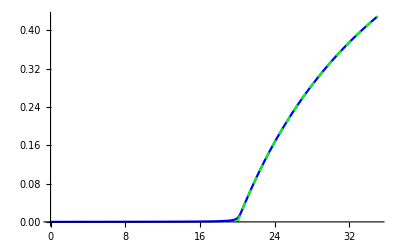

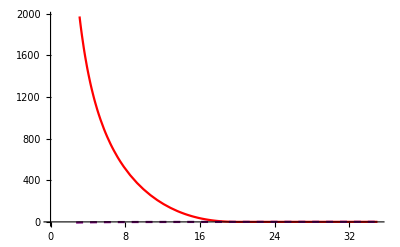

```mathematica
Show[PlotH,PlotHSS]
Show[PlotF,PlotFSS]
```

Due to the extreme magnitude a log plot makes the plot more clear and allows F and H to be plotted in the same figure

```mathematica
PlotLnH=Plot[Log[H[r]]/.plotsol[[1]],{r,plotrangemin,plotrangemax},PlotStyle->Blue,PlotRange->{-15,15}];
PlotLnF=Plot[Log[F[r]]/.plotsol[[1]],{r,plotrangemin,plotrangemax},PlotStyle->Red,PlotRange->{-15,15}];
PlotLnSS=Plot[Log[SSF[r]],{r,plotrangemin,plotrangemax},PlotStyle->Black,PlotRange->{-15,15}];
```

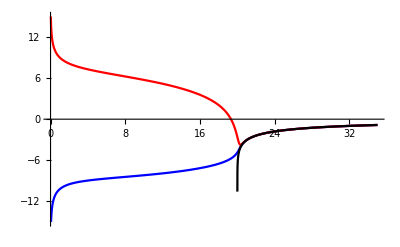

```mathematica
Show[PlotLnH,PlotLnF,PlotLnSS]
```

### Fitting the solution to theoretical integer scaling

As discussed in the thesis, the scaling of the solutions near the termination point should in theory go according to certain integer values. We can do this by first extracting the exact data points from the numerical solution.
plotsol[[1]][[2]][[2]][[3]][[1]] holds the r value for all computed data points. Getting the first fifty can be done as following

```mathematica
rlistfitF=plotsol[[1]][[2]][[2]][[3]][[1]][[1;;50]];
rlistfitH=plotsol[[1]][[1]][[2]][[3]][[1]][[1;;50]];
```

These are of course identical. We can also extract the values of both F and H at these data points:

```mathematica
fitFvalues=plotsol[[1]][[2]][[2]][[4]][[1;;50,1]];
fitHvalues=plotsol[[1]][[1]][[2]][[4]][[1;;50,1]];
```

With these we can recreate the data points to be used by the fitting function (including taking the log):

```mathematica
fitFpoints ={rlistfitF,Log[fitFvalues]}//Transpose;
fitHpoints ={rlistfitH,Log[fitHvalues]}//Transpose;
```

A fit is then performed using the function NonlinearModelFit[] :

```mathematica
NonlinearModelFit[fitFpoints,cF+s*Log[r],{cF,s},r]
```

FittedModel[-2.33325764705127476401739010551×10^33-«60» Log[r]]